```mathematica
ClearAll[ρ,nrho,rcrho,α,β]
```

```mathematica
ρ[r_,nrho_,rcrho_,α_,β_]=nrho^2 * (r/rcrho)^(-1/2*α) / (1 + (r/rcrho)^2)^(3/2 * β - 1/4*α)
```

nrho^2 (1+r^2/rcrho^2)^(α/4-(3 β)/2) (r/rcrho)^(-α/2)

```mathematica
Manipulate[
LogLogPlot[ρ[r,nrho,rcrho,α,β],{r,0.001,1},PlotRange->{0,1}],
{{nrho,1},0.1,2.0,0.01},
{{rcrho,0.15},0.1,0.2,0.01},
{{α,0.8},0.1,1.0,0.01},
{{β,0.7},0.1,1.0,0.01}
]
```

```mathematica
ClearAll[T,nT,rcT,a,b]
```

```mathematica
T[r_,nT_,rcT_,a_,b_]=nT * (1+a*r/rcT) / ((1+(r/rcT)^2)^b)
```

nT (1+r^2/rcT^2)^-b (1+(a r)/rcT)

```mathematica
Manipulate[
LogLinearPlot[T[r,nT,rcT,a,b],{r,0.01,1},PlotRange->{0,13}],
{{nT,5},5,5},
{{rcT,0.15},0.0,1.0,0.02},
{{a,2.5},0.0,5.0,0.02},
{{b,0.7},0.0,2.0,0.02}
]
```

```mathematica
ClearAll[bovera,a,b,α,β]
```

```mathematica
bovera[a_,α_,β_]=β+a*α
```

a α+β

```mathematica
Manipulate[
Plot[bovera[a,α,β],{a,0.01,1},PlotRange->Automatic],
{{α,-3},-5,5,0.1},
{{β,3},-3,3,0.1}
]
```

```mathematica
Manipulate[
Graphics[Circle[{0,0},{a*(β+a*α),a}]],
{{a,0.5},0,1,0.01},
{{α,-3},-5,5,0.1},
{{β,3},-3,3,0.1}
]
```

```mathematica
ClearAll[a,b,α,β]
```

```mathematica
(*radii={0.25,0.4,0.6,0.8,1.};*)
radii=Table[x/12,{x,1,2,1}]
```

{1/12,1/6}

```mathematica
radii[[Range[2,5]]]
```

{0.4,0.6,0.8,1.}

```mathematica
(*Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}];*)
Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}];
```

```mathematica
Graphics[%];
```

```mathematica
Manipulate[
Graphics[Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}],Axes->True],
{{α,2},-5,5,0.1},
{{β,1},-5,5,0.1}
]
```

```mathematica
ClearAll[a,b,α,β]
```

```mathematica
b[a_,α_,β_]=a*(β+a*α)
```

a (a α+β)

```mathematica
k[a_,ann_]=1 - ann^2 / a^2
```

1-ann^2/a^2

```mathematica
vs[a_,α_,β_]=4/3*Pi * a^2 * b[a,α,β]
```

4/3 a^3 π (a α+β)

```mathematica
ve[a_,ann_,α_,β_]=1/3*Pi * a^2 * b[a,α,β]*( 2-3*Sqrt[k[a,ann]] + Sqrt[k[a,ann]]^3 )
```

1/3 a^3 (2-3 √(1-ann^2/a^2)+(1-ann^2/a^2)^(3/2)) π (a α+β)

```mathematica
vc[a_,ann_,α_,β_]=2*Pi * ann^2 * b[a,α,β] * Sqrt[k[a,ann]]
```

2 a ann^2 √(1-ann^2/a^2) π (a α+β)

```mathematica
vcut[a_,ann_,α_,β_]=2*ve[a,ann,α,β] + vc[a,ann,α,β]
```

2 a ann^2 √(1-ann^2/a^2) π (a α+β)+2/3 a^3 (2-3 √(1-ann^2/a^2)+(1-ann^2/a^2)^(3/2)) π (a α+β)

```mathematica
vol[r_,is_,ia_,α_,β_]= 
If[ia==1 && is ==1,vs[r[[1]],α,β],
If[ia==1,vcut[r[[is]],1,α,β] - vcut[r[[is-1]],1,α,β],
If[ia==is,vs[r[[ia]],α,β]-vcut[r[[is]],r[[ia-1]],α,β],
vcut[r[[is]],r[[ia]],α,β]-vcut[r[[is]],r[[ia-1]],α,β]- (vcut[r[[is-1]],r[[ia]],α,β]-vcut[r[[is-1]],r[[ia-1]],α,β])]]];
```

```mathematica
Manipulate[
Table[vol[radii,is,ia,α,β],{ia,1,is,1}],
{{is,1},1,Length[radii],1},
{{α,2},-5,5,0.1},
{{β,1},-5,5,0.1}
]
```

```mathematica
Manipulate[
vcut[a,0.25,α,β],
{{a,0.1},0.1,1,0.1},
{{α,2},-5,5,0.1},
{{β,1},-5,5,0.1}
]
```

```mathematica
Manipulate[
Annulus=1;
Volumes=Table[vcut[a,radii[[Annulus]],α,β],{a,radii[[Range[Annulus,Length[radii]]]]}];
FitLinear=LinearModelFit[Volumes,{x,x^2},x];
Graphics[
Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}],Axes->True],
{{α,2},-5,5,0.1},
{{β,1},-5,5,0.1},
Dynamic[
Show[
ListPlot[Volumes,PlotRange->Automatic],
Plot[FitLinear[x],{x,1,Length[radii]}],
ImageSize->400
]
],
Dynamic[Show[
ListPlot[FitLinear["FitResiduals"],Frame->True,Filling->Axis,PlotRange->{-0.03,0.03}],
ImageSize->400]
]
]
```

```mathematica
ClearAll[is,ia,α,β];
```

```mathematica
Manipulate[
Plots=Table[ListPlot[Table[vol[radii,is,ia,α,β],{ia,1,is,1}],Joined->True],{is,1,Length[radii],1}];
Graphics[
Table[Circle[{0,0},{a*(β+a*α),a}],{a,radii}],Axes->True],
{{α,2},-5,5,0.1},
{{β,1},-5,5,0.1},
Dynamic[
Show[
Plots,
PlotRange->Automatic,
ImageSize->800,
AxesLabel->{"iShell","volume"}
]
]
]
```

Part::partw: Part 5 of {1/12, 1/6} does not exist.

Part::partw: Part 4 of {1/12, 1/6} does not exist.

Part::partw: Part 5 of {1/12, 1/6} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Table::iterb: Iterator {ia, 1, is, 1} does not have appropriate bounds.

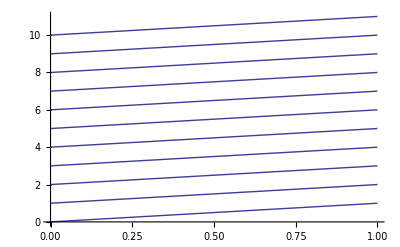

```mathematica
Show[Table[Plot[x+a,{x,0,1}],{a,0,10,1}],PlotRange->Automatic]
```